# Q3

{{-2,0},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{1,-2},{1,-1},{1,0},{1,1},{1,2},{2,0}}

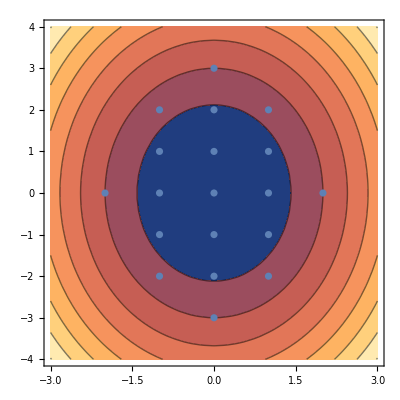

```mathematica
f[x_,y_]:=x^2/a^2+y^2/b^2-1
(*i*)
a=Input[];
b=Input[];
(*ii*)
pts = {};
Do[
Do[
If[
f[x,y]<=0,
AppendTo[
pts,
{x,y}
]
],
{y,-b,b}
],
{x,-a,a}
]
pts
(*iii*)
t1 =ContourPlot[f[x,y],{x,-a-1,a+1},{y,-b-1,b+1}];
p1=ListPlot[pts];
Show[t1,p1]
```